# C-SemigroupsToolbox

Descripción : Este notebook contiene un conjunto de funciones desarrolladas en Mathematica para trabajar, visualizar y crear ejemplos de C-semigrupos en N.b2. Para ello, nos ayudamos del paquete Normaliz. Es una herramienta de código abierto para cálculos en monoides afines, configuraciones vectoriales, politopos de retículo y conos racionales. Normaliz también calcula poliedros algebraicos, es decir, poliedros definidos sobre extensiones algebraicas reales de Q. https://www.normaliz.uni-osnabrueck.de/

Autores :
  	- Sanchez  Loureiro, Adrián.
   	- Vigneron  Tenorio, Alberto.
 
Licencia : GPL-3.0
  
Repositorio :  https://github.com/asanlou/C-SemigroupsToolbox

## Funciones

Algo de racionalizar

```mathematica
(*ES PARA EJECUTAR EN LOCAL Y CALCULAR CON NORMALIZ LA BASE DE HILBERT Y LAS ECUACIONES DEL CONO INICIAL!!!*)
toRat[x_]:=Module[{num,den,xx,a,b},
(*Pasa los racionales a numerador/denominador*)
(*Output: el par {numerador, denominador}*)
xx=Rationalize[x];
a=Numerator[xx];
b=Denominator[xx];
Return[{a,b}]
];
```

```mathematica
RationalToInt[V_]:=Module[{l=Length[V],i,mcm,V1},
(*pasa un vector racional al menor proporcional entero*)
V1=Table[{toRat[V[[i]]][[1]],toRat[V[[i]]][[2]]},{i,l}];
mcm=LCM @@ Table[V1[[i,2]],{i,l}];
V1=Table[mcm*V1[[i]][[1]]/V1[[i]][[2]],{i,l}];
Return[V1]
];
```

Generando Cono

```mathematica
ConeGenSupHyp[rayos_,dirTrab_]:=Module[{Nf,Nc,origen,f,i,cad="",ratray,suphyp,gen,st1,st2,caux,lineas={}},

{Nf,Nc}=Dimensions[rayos];

origen=Table[0,{i,Nc}];

ratray=Table[RationalToInt[rayos[[i]]],{i,Nf}];

(*Escribir cono .in para Normaliz*)
cad="amb_space "<> ToString[Nc]<>"\n";
cad=cad<>"cone "<>ToString[Nf]<>"\n";
For[i=1,i≤Nf,i++,
cad=cad<>StringReplace[ToString[ratray[[i]]],{", "-> " ","{"->"","}"->""}]<>"\n";
];
cad=cad<>"vertices "<>ToString[1]<>"\n";
cad=cad<>StringReplace[ToString[origen],{", "-> " ","{"->"","}"->" "}]<>"1";
f=OpenWrite[dirTrab<>"aux1.in"];
WriteString[f,cad];
Close[f];
Run["normaliz -c -N -a "<>dirTrab<>"aux1.in"];
cad=ReadString[dirTrab<>"aux1.gen"];
st1=StringToStream[cad];
caux=ReadLine[st1];
caux=ReadLine[st1];
caux=ReadLine[st1];
While[Characters[caux]≠{},
		AppendTo[lineas,caux];
		caux=ReadLine[st1];
	];
gen=Flatten[ImportString[#,"Table"]& /@lineas,1];
gen=Select[gen,#[[Length[gen[[1]]]]]==0&];
For[i=1,i≤ Length[gen],i++,
gen[[i]]=Delete[gen[[i]],Nc+1];
];
(*seleciona generadores*)
cad="";
cad=ReadString[dirTrab<>"aux1.cst"];
st2=StringToStream[cad];
lineas={};
origen=Interpreter["Number"][ReadLine[st2]];
caux=ReadLine[st2];
i=1;
While[i≤origen,
caux=ReadLine[st2];
AppendTo[lineas,caux];
i++
];
suphyp=Flatten[ImportString[#,"Table"]& /@lineas,1];
suphyp=Select[suphyp,#[[Length[suphyp[[1]]]]]==0&]; (*seleciona planos soporte*)
For[i=1,i≤ Length[suphyp],i++,
suphyp[[i]]=Delete[suphyp[[i]],Nc+1];
];

Return[{gen,suphyp}] (*Devuelve base de Hilbert (gen) e hiperplanos soportes (suphyp) *)
];
```

Comprueba punto en Cono

```mathematica
InCone[pto_,Eq_]:=Module[{prod,verif},
(*Verifica si un pto está en el cono dado por las inecuaciones Eq*)
prod=Eq.pto;
verif=Table[prod[[i]]≥ 0,{i,Length[prod]}];
verif=Union[verif];
If[verif== {True},Return[True],Return[False]];
];
```

Conjuntos de un C-Semigrupo

## Apery(S,b)

#### Apery(S,b) conocido Gaps y Eq Cono

```mathematica
GetAperyEq[b_,Gaps_,Eq_] := Module[{nGaps,i,aux,Apery},
(*Compruebo que b no es un hueco*)
If[( MemberQ[Gaps,b]),
(*If*)
	Print[b,"no pertenece al C-semigrupo."];
	Return[{}],

(*Else*)
	(*Compruebo que b está en el cono*)
	If[¬ InCone[b,Eq],
		Print[b,"no pertenece al cono"];
		Return[{}]
];
];

(*Número de huecos y inicializando conjunto Apery*)
nGaps = Length[Gaps];
Apery={};

(*Puntos Apery : punto x del C-semigrupo tal que x-b pertenece a Gaps.*)
(*Equivalentemente, los puntos g de Gaps tal que g+b está en el cono y no pertenece a Gaps.*)
(*Calculamos el Apery a partir de estos últimos:*)
For[i=1,i≤ nGaps,i++,
aux=b+Gaps[[i]];
If[(¬MemberQ[Gaps,aux]),
Apery = Append[Apery,aux];
];
];

(*Devolvemos Apery obtenido*)
Return[Apery]

];
```

#### Apery(S,b) conocido geners del CSemi y Gaps y FileDirectory

```mathematica
GetApery[b_,GenSemig_,Gaps_,dirTrab_] := Module[{nGaps,i,aux,Apery,T1,LineasT1,vectorsinrays,T1L,Eq},
(*Compruebo que b no es un hueco*)
If[( MemberQ[Gaps,b]),
Print[b,"no pertenece al C-semigrupo."];
Return[{}]
];

(*Calculamos ecuaciones del cono para usar función InCone*)
(**Vectores de los rayos extremales para sacar ecuaciones del cono**)
T1=ConvexHullMesh[Join @@ {{{0,0}},GenSemig}];
LineasT1=MeshPrimitives[T1,1];
	T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];

(**Ecuaciones del cono para comprobar si punto está en el cono**)
Eq=ConeGenSupHyp[vectorsinrays,dirTrab][[2]];

(*Compruebo que b está en el cono*)
If[¬ InCone[b,Eq],
Print[b,"no pertenece al cono"];
Return[{}]
];

(*Inicializando conjunto Apery*)
Apery={};

(* Puntos Apery : punto x del C-semigrupo tal que x-b pertenece a Gaps.
De forma similar los puntos g de Gaps tal que g+b está en el cono y no pertenece a Gaps. 
Calculamos el Apery a partir de estos últimos: *)
nGaps = Length[Gaps];

For[i=1,i≤ nGaps,i++,
aux=b+Gaps[[i]];
If[(¬MemberQ[Gaps,aux]),
Apery = Append[Apery,aux];
];
];

(*Devolvemos Apery obtenido*)
Return[Apery]
];
```

## PseudoFrobs a partir de generadores y huecos

```mathematica
GetPseudoFrobenius[GenSemig_,Gaps_] := Module[{nGaps,i,j,nGens,PseuFrobs},
 nGens = Length[GenSemig];
nGaps = Length[Gaps];
PseuFrobs={};

For[i=1,i≤ nGaps,i++,
	j=1;

	While[(j ≤ nGens)∧ (¬MemberQ[Gaps,Gaps[[i]]+GenSemig[[j]] ]) ,
		j++

	];

	If[ j == nGens+1, 
		PseuFrobs = Append[PseuFrobs,Gaps[[i]]]
	];
];
Return[PseuFrobs]

];
```

## Especial Gaps a partir de Pseudos y Huecos

```mathematica
GetEspGaps[PseuFrobs_,Gaps_] := Module[{EspGaps,i,nPseu},
 nPseu = Length[PseuFrobs];
EspGaps={};

For[i=1,i≤ nPseu,i++,
	If[¬MemberQ[Gaps,2*PseuFrobs[[i]]],
			 EspGaps = Append[EspGaps,PseuFrobs[[i]]]
	];
];

Return[EspGaps]
];
```

## Especial Gaps y n.ba de ellos a partir de Generadores y Huecos

```mathematica
GetEspGapsGen[GenSemig_,Gaps_] := Module[{nGaps,i,j,nGens,EspGaps},
 nGens = Length[GenSemig];
nGaps = Length[Gaps];
EspGaps={};

For[i=1,i≤ nGaps,i++,
	j=1;

	While[(j ≤ nGens)∧ (¬MemberQ[Gaps,Gaps[[i]]+GenSemig[[j]] ]) ,
		j++

	];

	If[ (j == nGens+1)∧(¬MemberQ[Gaps,2*Gaps[[i]]]), 
		EspGaps = Append[EspGaps,Gaps[[i]]]
	];
];
Return[EspGaps]

];
```

## Fund Gaps a partir de huecos

```mathematica
GetFundGaps[Gaps_] := Module[{FundGaps,i,nGaps},
nGaps = Length[Gaps];
FundGaps={};

For[i=1,i≤ nGaps,i++,
	If[(¬MemberQ[Gaps,2*Gaps[[i]]])∧(¬MemberQ[Gaps,3*Gaps[[i]]]),
			 FundGaps = Append[FundGaps,Gaps[[i]]]
	];
];

Return[FundGaps]
];
```

## I(n) = { s ∈ S : s \le _\CaC n }$

#### I(n) conocido Gaps y Eq Cono

```mathematica
GetIsetEq[n_,GenSemig_,Gaps_,Eq_] :=  Module[{Iset,T1,LineasT1,vectorsinrays,T1L,i,j},
(*Puntos I(n) : puntos x del C-semigrupo tal que n - x pertenece al cono.*)
(*Equivalentemente, los (x1,x2) con x1 <= n1 y x1 <= n2, que que cumplen la definicion de I(n)*)
(*Calculamos el I(n) bajo ese critero:*)

(*Compruebo que n está en el cono*)
If[¬ InCone[n,Eq],
	Print[n,"no pertenece al cono"];
	Return[{}]
];

(*Inicializando I(n) -> coordenadas menores que las de n.*)
Iset=Flatten[ParallelTable[{i,j},{i,0,n[[1]]},{j,0,n[[2]]}],1];

(*Tomando puntos del cono*)
Iset=Select[Iset,InCone[#,Eq]&];

(*Tomando puntos de Iset*)
Iset = Complement[Iset,Gaps];

Iset=Select[Iset,InCone[n-#,Eq]&];

(*Devolviendo Iset*)
Return[Iset]
];
```

(*Vectores de los rayos extremales para sacar ecuaciones del cono*)
(*Hacemos el cierre convexo de los generadores y  despues vmoas afinando.*)
T1 = ConvexHullMesh[Join @@ {{{0, 0}}, GenSemig}];

(*Mesh hace del vierre convexo, coge las aristas*)
LineasT1 = MeshPrimitives[T1, 1];

(*Las aristas las dan por sus vertices, luego nos quedamos solo con las que pasan por el origen*)
T1L = Select[Level[LineasT1, {2}], MemberQ[#, {0., 0.}] &];

(*Vectores de rayos del cono*)
(*De las aristas nos quedamos con los puntos del final del cierre y cogemos los vectores.*)
vectorsinrays = Select[Flatten[T1L, 1], # != {0., 0.} &];

#### I(n) conocido geners del CSemi y Gaps y FileDirectory

In this work, we consider different orders on some sets. On a non-empty set $L\subset \N^p$, consider the partial order $x \le_L y$ if $y- x \in L$, with $x,y \in L$.

```mathematica
GetIsetNoEq[n_,GenSemig_,Gaps_,dirTrab_] := Module[{Iset,T1,LineasT1,vectorsinrays,nGaps,T1L,Eq,auxGaps,i,j},
(*Puntos I(n) : puntos x del C-semigrupo tal que n - x pertenece al cono.*)
(*Equivalentemente, los (x1,x2) con x1 <= n1 y x1 <= n2, que pertenecen al cono y no pertenecen a Gaps.*)
(*Calculamos el I(n) bajo ese critero:*)

(*Vectores de los rayos extremales para sacar ecuaciones del cono*)
T1=ConvexHullMesh[Join @@ {{{0,0}},GenSemig}];
LineasT1=MeshPrimitives[T1,1];
	T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];

(*Ecuaciones del cono para comprobar si punto está en el cono*)
Eq=ConeGenSupHyp[vectorsinrays,dirTrab][[2]];

(*Compruebo que n está en el cono*)
If[¬ InCone[n,Eq],
	Print[n,"no pertenece al cono"];
	Return[{}]
];

(*Inicializando I(n) -> coordenadas menores que las de n.*)
Iset=Flatten[ParallelTable[{i,j},{i,0,n[[1]]},{j,0,n[[2]]}],1];

(*Tomando puntos del cono*)
Iset=Select[Iset,InCone[#,Eq]&];

(*Tomando puntos de Iset*)
Iset = Complement[Iset,Gaps];

Iset=Select[Iset,InCone[n-#,Eq]&];

(*Devolviendo Iset*)
Return[Iset]
];
```

## C(S_i) = { h ∈ SG(S) : h ∉ S_i }

```mathematica
IrreducibleCSi[Semig_, DescGaps_] := Module[{espGaps,cSi},
	(*Puntos I(n) : puntos x del C-semigrupo tal que n - x pertenece al cono.*)
	(*Equivalentemente, los (x1,x2) con x1 <= n1 y x1 <= n2, que que cumplen la definicion de I(n)*)
	(*Calculamos el I(n) bajo ese critero:*)

	espGaps = GetEspGaps[GetPseudoFrobenius[Semig[[1]],Semig[[2]]],Semig[[2]]];
	
	cSi = Intersection[espGaps, DescGaps];
	
	(*Devolviendo Iset*)
	Return[cSi]
];
```

Algunas funciones para órdenes

```mathematica
OrdenAleatorio[f_]:=Module[{M},
M=Join[RandomInteger[{1,10},{1,f}],RandomInteger[{-10,10},{f-1,f}]];
While[Det[M]==0,
M=Join[RandomInteger[{1,10},{1,f}],RandomInteger[{-10,10},{f-1,f}]];
];
Return[M];
];
```

```mathematica
OrdenCrear[f_]:=Module[{M},
M=Join[RandomInteger[{1,10},{1,f}],RandomInteger[{-10,10},{f-1,f}]];
While[Det[M]==0,
M=Join[RandomInteger[{1,10},{1,f}],RandomInteger[{-10,10},{f-1,f}]];
];
Return[M];
];
```

vector Frobenius y conjunto N(S)

## Lexicografico graduado inverso

```mathematica
FrobeniusDRLexi[hole_]:=Module[{i,j,x,X,MonHole,Frob},
(*hole lista de huecos*)
(*Devuelve Frobnenius respecto orden fijado*)
X=Table[Subscript[x, i],{i,Length[hole[[1]]]}];
MonHole=Sum[Product[(Subscript[x, i])^hole[[j]][[i]],{i,1,Length[hole[[j]]]}],{j,1,Length[hole]}];
(*Print["Polinomio= ",MonHole];*)
MonHole=MonomialList[MonHole,X,DegreeReverseLexicographic];
Frob=MonHole[[1]];(*Éste es el Fröbnenius respecto al orden fijado*)
Frob=Table[Exponent[Frob,Subscript[x, i]],{i,Length[hole[[1]]]}];
Return[Frob];
];
```

## Lexicografico graduado

```mathematica
FrobeniusDLexi[hole_]:=Module[{i,j,x,X,MonHole,Frob},
(*hole lista de huecos*)
(*Devuelve Frobnenius respecto orden fijado*)
X=Table[Subscript[x, i],{i,Length[hole[[1]]]}];
MonHole=Sum[Product[(Subscript[x, i])^hole[[j]][[i]],{i,1,Length[hole[[j]]]}],{j,1,Length[hole]}];
(*Print["Polinomio= ",MonHole];*)
MonHole=MonomialList[MonHole,X,DegreeLexicographic];
Frob=MonHole[[1]];(*Éste es el Fröbnenius respecto al orden fijado*)
Frob=Table[Exponent[Frob,Subscript[x, i]],{i,Length[hole[[1]]]}];
Return[Frob];
];
```

## Lexicografico

```mathematica
FrobeniusLexi[hole_]:=Module[{i,j,x,X,MonHole,Frob},
(*hole lista de huecos*)
(*Devuelve Frobnenius respecto orden fijado*)
X=Table[Subscript[x, i],{i,Length[hole[[1]]]}];
MonHole=Sum[Product[(Subscript[x, i])^hole[[j]][[i]],{i,1,Length[hole[[j]]]}],{j,1,Length[hole]}];
(*Print["Polinomio= ",MonHole];*)
MonHole=MonomialList[MonHole,X,Lexicographic];
Frob=MonHole[[1]];(*Éste es el Fröbnenius respecto al orden fijado*)
Frob=Table[Exponent[Frob,Subscript[x, i]],{i,Length[hole[[1]]]}];
Return[Frob];
];
```

## Dando matriz de pesos

```mathematica
Frobenius2[hole_,MatrizOrden_]:=Module[{i,p=Length[hole],MonHole,MonHole2,MonHole3,Frob},
(*hole lista de huecos*)
(*Devuelve Frobnenius respecto orden fijado por la matriz*)
MonHole=Table[MatrizOrden.hole[[i]],{i,1,p}];
MonHole2=Sort[MonHole];
(*Print["Polinomio= ",MonHole,MonHole2];*)
MonHole3=Flatten[Position[MonHole,MonHole2[[p]]],1];
(*Print["Polinomio= ",MonHole3];*)
Frob=hole[[MonHole3[[1]]]];(*Éste es el Fröbnenius respecto al orden fijado*)
Return[Frob];
];
```

## N(S)=={x∈S|x⪯F(S)}

#### Lexicografico graduado inverso

```mathematica
NFrobeniusDRLexi[GenSemig_,Gaps_]:=Module[{semig, L,T1,LineasT1,T1L,vectorsinrays,t,ConeC,i,j,
Frob1,x,X,MonHole,MonHoleFixed,elemLength},
(*Calcula N(S) a partir de sus generadores minimales, huecos y el Frobenius.
Para ello, calcula parte del semigrupo y se ordena quedándonos con N(S)*)

semig=GenSemig;
L=Length[semig];

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

elemLength=Length[ConeC[[1]]];

ConeC=Union[ConeC[[2;;]],Gaps];

X=Table[Subscript[x, i],{i,elemLength}];
MonHole=Sum[Product[(Subscript[x, i])^ConeC[[j]][[i]],{i,1,elemLength}],{j,1,Length[ConeC]}];

MonHole=MonomialList[MonHole,X,DegreeReverseLexicographic];

MonHoleFixed=Table[Table[Exponent[MonHole[[j,i]],Subscript[x, i]],{i,elemLength}],{j,Length[MonHole]}];

Frob1 = FrobeniusDRLexi[Gaps];

If[Position[MonHoleFixed,Frob1]!={},
MonHoleFixed = MonHoleFixed[[Position[MonHoleFixed,Frob1][[1,1]]+1;;]];
Return[Complement[MonHoleFixed,Gaps]],
Return[{}]
]


];
```

#### Lexicografico graduado

```mathematica
NFrobeniusDLexi[GenSemig_,Gaps_]:=Module[{semig, L,T1,LineasT1,T1L,vectorsinrays,t,ConeC,i,j,
Frob1,x,X,MonHole,MonHoleFixed,elemLength},
(*Calcula N(S) a partir de sus generadores minimales, huecos y el Frobenius.
Para ello, calcula parte del semigrupo y se ordena quedándonos con N(S)*)

semig=GenSemig;
L=Length[semig];

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

elemLength=Length[ConeC[[1]]];

ConeC=Union[ConeC[[2;;]],Gaps];

X=Table[Subscript[x, i],{i,elemLength}];
MonHole=Sum[Product[(Subscript[x, i])^ConeC[[j]][[i]],{i,1,elemLength}],{j,1,Length[ConeC]}];

MonHole=MonomialList[MonHole,X,DegreeLexicographic];

MonHoleFixed=Table[Table[Exponent[MonHole[[j,i]],Subscript[x, i]],{i,elemLength}],{j,Length[MonHole]}];

Frob1 = FrobeniusDLexi[Gaps];

If[Position[MonHoleFixed,Frob1]!={},
MonHoleFixed = MonHoleFixed[[Position[MonHoleFixed,Frob1][[1,1]]+1;;]];
Return[Complement[MonHoleFixed,Gaps]],
Return[{}]
]


];
```

#### Lexicografico

```mathematica
NFrobeniusLexi[GenSemig_,Gaps_]:=Module[{semig, L,T1,LineasT1,T1L,vectorsinrays,t,ConeC,i,j,
Frob1,x,X,MonHole,MonHoleFixed,elemLength},
(*Calcula N(S) a partir de sus generadores minimales, huecos y el Frobenius.
Para ello, calcula parte del semigrupo y se ordena quedándonos con N(S)*)

semig=GenSemig;
L=Length[semig];

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

elemLength=Length[ConeC[[1]]];

ConeC=Union[ConeC[[2;;]],Gaps];

X=Table[Subscript[x, i],{i,elemLength}];
MonHole=Sum[Product[(Subscript[x, i])^ConeC[[j]][[i]],{i,1,elemLength}],{j,1,Length[ConeC]}];

MonHole=MonomialList[MonHole,X,Lexicographic];

MonHoleFixed=Table[Table[Exponent[MonHole[[j,i]],Subscript[x, i]],{i,elemLength}],{j,Length[MonHole]}];

Frob1 = FrobeniusLexi[Gaps];

If[Position[MonHoleFixed,Frob1]!={},
MonHoleFixed = MonHoleFixed[[Position[MonHoleFixed,Frob1][[1,1]]+1;;]];
Return[Complement[MonHoleFixed,Gaps]],
Return[{}]
]


];
```

Algo de conjetura de Wilf con Frobenius

```mathematica
WilfMatrizOrdenAleatoria[gen_,hole_,dirTrab_,rayos_,info_]:=(*Versión para No N^p completo, poliedro ajustado a rayos para latte y normaliz!!*)Module[{i,Frob,sumF,VertConv,pesos,p=Length[hole[[1]]],VertConvLatte,cad,f,st1,ptoIn=0,lineas={},caux,ptohip,x,MonHip,MonHip2,posFrobHip,MatrizOrden,posFrobHip2,nombre},
(*hole lista de huecos*)
(*Devuelve todos los elementos de N^p por debajo de Frobenius respecto a un orden fijado "DegreeLexicographic"*)

(*MatrizOrden={{1,1},{1,0}};*)
MatrizOrden=OrdenAleatorio[p];
If[info,Print["Matriz de orden= ",MatrizOrden]];

Frob=Frobenius2[hole,MatrizOrden];(*Frobnenius*)
pesos=MatrizOrden[[1]];
sumF=Sum[Frob[[i]]*pesos[[i]],{i,p}];
VertConv=Table[sumF*rayos[[i]],{i,Length[rayos]} ];
VertConvLatte=Table[Prepend[VertConv[[i]],pesos.rayos[[i]]],{i,Length[rayos]}];
(*Print["pesos= ",pesos, " Frob= ",Frob," suma= ",sumF, " vértices= ",VertConv," vertices para Latte= ",VertConvLatte];*)
cad=ToString[Length[VertConvLatte]+1]<>" "<>ToString[p+1]<>"\n";
cad=cad<>ToString[1];
For[i=1,i≤p,i++,
cad=cad<>" "<>ToString[0];
];
cad=cad<>"\n";
For[i=1,i≤Length[VertConvLatte],i++,
cad=cad<>StringReplace[ToString[VertConvLatte[[i]]],{", "-> " ","{"->"","}"->""}]<>"\n";
];
f=OpenWrite[dirTrab<>"auxlatte2.vrep_latte"];
WriteString[f,cad];
Close[f];
Pause[.2];
ptoIn=<<"!C:/latte-integrale-1.7.3/dest/bin/count.exe --vrep D:\Dropbox\Publicaciones\Csemigroup\calculos\auxlatte2.vrep_latte";
(*Print["Número de puntos en el convexo= ",ptoIn];*)
(*nombre="D:/Dropbox/Publicaciones/Csemigroup/calculos/"<>" count --vrep auxlatte.vrep_latte";
Print[nombre];
Run[nombre];
(*Run["count.exe --vrep " <>dirTrab<>"auxlatte.vrep_latte"];*)
cad=ReadString[dirTrab<>"numOfLatticePoints"];
st1=StringToStream[cad];
ptoIn=ToExpression[ReadLine[st1]];
*)
(*METO SALIDA EN ptoIn*)
(*YA ESTARÍAN CONTADOS TODOS LOS NATURALES QUE ESTÁN EN EL HIPERPLANO Y POR DEBAJO DEL HIPERPLANO QUE CONTIENE A Frob*)
VertConvLatte=Table[Append[VertConv[[i]],pesos.rayos[[i]]],{i,Length[rayos]}];(*Convierte para normaliz*)
cad="";
cad="amb_space "<> ToString[p]<>"\n";
cad=cad<>"vertices "<>ToString[Length[VertConvLatte]]<>"\n";
For[i=1,i≤Length[VertConvLatte],i++,
cad=cad<>StringReplace[ToString[VertConvLatte[[i]]],{", "-> " ","{"->"","}"->""}]<>"\n";
];
Pause[.1];
f=OpenWrite[dirTrab<>"auxhiper2.in"];
WriteString[f,cad];
Close[f];
Run["normaliz -c -N -a "<>dirTrab<>"auxhiper2.in"];
cad=ReadString[dirTrab<>"auxhiper2.gen"];
st1=StringToStream[cad];
caux=ReadLine[st1];
caux=ReadLine[st1];
caux=ReadLine[st1];
While[Characters[caux]≠{},
		AppendTo[lineas,caux];
		caux=ReadLine[st1];
	];
ptohip=Flatten[ImportString[#,"Table"]& /@lineas,1];
ptohip=Select[ptohip,#[[Length[ptohip[[1]]]]]==1&];
For[i=1,i≤ Length[ptohip],i++,
ptohip[[i]]=Delete[ptohip[[i]],p+1];
];

MonHip=Table[MatrizOrden.ptohip[[i]],{i,1,Length[ptohip]}];
MonHip2=Sort[MonHip];

(*MonHip=Flatten[Table[Position[MonHip,MonHip2[[i]]],{i,Length[MonHip2]}],1];
ptohip=Flatten[Table[ptohip[[MonHip[[i]]]],{i,Length[ptohip]}],1];
posFrobHip=Position[ptohip,Frob][[1]][[1]];
Print[MonHip2,MatrizOrden,Frob,MatrizOrden.Frob];*)

(*Print[" aqui-> ",MonHip2,MatrizOrden,Frob,MatrizOrden.Frob];*)
posFrobHip2=Position[MonHip2,MatrizOrden.Frob][[1]][[1]];
(*Print["Ptos en hiperplano= ",ptohip,"\n ptos. en convexo= ",ptoIn];
Print["pos de Frob1= ",posFrobHip,"pos de Frob2 en hiperplano= ",posFrobHip2];*)

(*Print["Aqui2-> ",Length[gen]," ptoIn= ",ptoIn," longPtohip= ",Length[ptohip]," longHole= ",Length[hole]];*)

(*Print[(*"Semigrupo= " ,gen, " huecos= ",hole, " Frob= ",Frob," Orden= ",MatrizOrden,"\n *)"Huecos= ",Length[hole],", e(S)= ",Length[gen],", n(S)= ",ptoIn-Length[ptohip]+posFrobHip2-Length[hole],", N(F(S))+1= ",(ptoIn-Length[ptohip]+posFrobHip2+1),", n(S)e(S)- (N(F(S))+1)= ",Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])-(ptoIn-Length[ptohip]+posFrobHip2+1),", n(S)e(S)/ (N(F(S))+1)= ",N[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])/(ptoIn-Length[ptohip]+posFrobHip2+1)]];*)
cociente=Join[cociente,{{{StringJoin["Huecos= ",ToString[Length[hole]],", e(S)= ",ToString[Length[gen]],", n(S)= ",ToString[ptoIn-Length[ptohip]+posFrobHip2-Length[hole]],", N(F(S))+1= ",ToString[(ptoIn-Length[ptohip]+posFrobHip2+1)],", n(S)e(S)- (N(F(S))+1)= ",ToString[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])-(ptoIn-Length[ptohip]+posFrobHip2+1)],", n(S)e(S)/ (N(F(S))+1)= ",ToString[N[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])/(ptoIn-Length[ptohip]+posFrobHip2+1)]]]},{N[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])/(ptoIn-Length[ptohip]+posFrobHip2+1)]}}}];
If[(Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])≥(ptoIn-Length[ptohip]+posFrobHip2+1))≠ True,
Print["NO WILF!!!!!! " (*,"semigrupo= " ,gen, " huecos= ",hole, " Frob= ",Frob," Orden= ",MatrizOrden *)];
];
NotebookSave[];

Return[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])≥(ptoIn-Length[ptohip]+posFrobHip2+1)];
];
```

Quita min gen en SN

```mathematica
MimRemoveOneGen[gen_,rgen_,H_,Eq_]:=Module[{gen0,gen1,min,i},
(*Calcula el sistema minimal de generadores de un semigrupo obtenido quitando al semigrupo mínimamente generado por "gen" el generador "rgen" ("rgen" tiene que pertenecer a "gen").
Eq son las ecuaciones del cono que contiene a <gen> y H los elementos que le faltan a <gen> para ser el cono*)
(*Print["Entrada MInRE..= ",gen," , ",rgen," , ",H," , ",Eq];*)
gen0=Complement[gen,{rgen}];
gen1=Table[gen0[[i]]+rgen,{i,Length[gen0]}];
gen1=Union[gen1,{2*rgen,3*rgen}];
min=MinGen[gen0,gen1,Union[H,{rgen}],Eq];(*Manda los de entrada y los generados por separado*)
Return[{min,Union[H,{rgen}]}]
(*Salida: conjunto formado por {generadores minimales, huecos respecto al cono inicial} *)
];
```

SemigroupGenusToDFromGenEqEnRamaSinQuitarDeEjesYEnCirculo

```mathematica
SemigroupGenusToDFromGenEqEnRamaSinQuitarDeEjesYEnCirculo[conegen_,coneEq_,dirTrab_,d_,rayos_,info_,cotaInf_,cotaSup_]:=Module[{hilb,Eq,SemGenD,i,j,allcase={},allcase1={},allcase2={},todej,suc,SemGenD2,time,medGen,mini,W=0,aux},
(* dd saco "dd" para hacer una barra dinámica*)
long={};
(* long variable global que recoge dimensión de inmersión de los semigrupos que aparecen *)
(*SI MatrizOrden=Matriz de orden, comprueba desigualdad de Wilf extendida para el orden implementado, =False no hace nada*)
hilb=conegen; (*Base de Hilbert del cono inicial*)
Eq=coneEq;(*Inecuaciones del cono inicial*)
SemGenD={{0,hilb,{}}};
If[info,Print["Número de semigrupos de ", 0," huecos= ",1, " número generadores minimals= ",Length[SemGenD[[1]][[2]]]];
];
suc={1};
long=Join[long,{Length[SemGenD[[1]][[2]]]}];
SemGenD=Join[SemGenD,{{1,ParallelMap[MimRemoveOneGen[hilb,#,{},Eq]&,hilb]}}];
(*El formato de SemGenD es uno inicial de las primeras pruebas. Ajustar para quitar el 0 y el 1 inicial. SemGenD2 ya no tiene ese número entero inicial*)
suc=Join[suc,{Length[SemGenD[[2,2]]]}];
SemGenD2=SemGenD[[2,2]];
(*Print["Semigrupos con n generadores= ",Select[SemGenD2,Length[#[[1]]]== 10&]];*)
(*Se toma un único semigrupo de forma aleatoria*)
SemGenD2=SemGenD2[[RandomInteger[{1,Length[SemGenD2]}]]];
For[dd=2,dd≤ d,dd++,
If[info,Print["Semigrupo seleccionado= ",SemGenD2, " n.ba huecos= ",Length[SemGenD2[[2]]]];
];
long=Join[long,{Length[SemGenD2[[1]]]}];
time=SessionTime[];
allcase=SemGenD2;

NotebookSave[];

SemGenD2={};
(*Todos los semigrupos con dd-1 huecos respecto al cono inicial. Cada semigrupo está determinado por {sistema minimal de generadores, huecos}*)
(*Print["SEMIGRUPOS DE ENTRADA= ",allcase];*)

(*Tomo un elemento aleatorio de sistema minimal para "hacer hueco" fuera de los ejes*)
aux=Select[allcase[[1]],(A[[1]][[2]]*#[[1]] - A[[1]][[1]]*#[[2]])*(A[[2]][[2]]*#[[1]] - A[[2]][[1]]*#[[2]])≠0 &&  (#[[1]])^2+(#[[2]])^2≤cotaSup&&cotaInf<(#[[1]])^2+(#[[2]])^2&];
If[aux≠{},
(*Rama aelatoria a partir del nodo*)
allcase2=Join[allcase,{{aux[[RandomInteger[{1,Length[aux]}]]]}}]; 
(*Print["SEmigrupos con efectivos antes de quitar= ",allcase2, " longitud= ",Length[allcase2]];*)

(*Se une a cada (generadores semi, hueco) los generadores efectivos, i.e. la estructura es (generadores semi, hueco, generadores efectivos)*)

(*Print["semigrupos con efectivos= ",allcase2, " longitud= ",Length[allcase2]];
Print["semigrupo 1= ",allcase2[[1]]];*)
allcase1=allcase2;
NotebookSave[];
(*Print["Mando a MimRemoveOneGen-> ",allcase1[[1]],"  ",allcase1[[3,1]],"  ",allcase1[[2]]];*)
SemGenD2=MimRemoveOneGen[allcase1[[1]],allcase1[[3,1]],allcase1[[2]],Eq] ;
(*Print[" Tiempo para ",dd," huecos (cálculo completo)= ",SessionTime[]-time];
Print["Semigrupos con multiplicidad mínima generadores= ",Select[SemGenD2,Length[#[[1]]]== 2*Length[conegen[[1]]]&]];*)
(*Print["Semigrupos con máximo número de generadores= ",Select[SemGenD2,Length[#[[1]]]== maxi&]];*)
(*Print["nuevo semigrupo= ",SemGenD2];*)
NotebookSave[];
,
Print["No generadores minimales en la circunferncia de radio =", cota];
Break[];
];
];
(*Print[SemGenD2];*)
Return[SemGenD2] (*SemGen2[1]= generadores del semigrupo, SemGen2[2]= huecos del semigrupo*)
];

(*En esta versión del programa sólo se guardan los semigrupos en ejecuación*)
```

SemigroupGenusToDFromGenEqEnRama

```mathematica
SemigroupGenusToDFromGenEqEnRama[conegen_,coneEq_,dirTrab_,d_,rayos_,info_]:=Module[{hilb,Eq,SemGenD,i,j,allcase={},allcase1={},allcase2={},todej,suc,SemGenD2,time,medGen,mini,W=0},
(* dd saco "dd" para hacer una barra dinámica*)
long={};
(* long variable global que recoge dimensión de inmersión de los semigrupos que aparecen *)
(*SI MatrizOrden=Matriz de orden, comprueba desigualdad de Wilf extendida para el orden implementado, =False no hace nada*)
hilb=conegen; (*Base de Hilbert del cono inicial*)
Eq=coneEq;(*Inecuaciones del cono inicial*)

SemGenD={{0,hilb,{}}};

If[info,
Print["Número de semigrupos de ", 0," huecos= ",1, " número generadores minimals= ",Length[SemGenD[[1]][[2]]]];
];

suc={1};

long=Join[long,{Length[SemGenD[[1]][[2]]]}];

SemGenD=Join[SemGenD,{{1,ParallelMap[MimRemoveOneGen[hilb,#,{},Eq]&,hilb]}}];
(*El formato de SemGenD es uno inicial de las primeras pruebas. Ajustar para quitar el 0 y el 1 inicial. SemGenD2 ya no tiene ese número entero inicial*)

suc=Join[suc,{Length[SemGenD[[2,2]]]}];

SemGenD2=SemGenD[[2,2]];
(*Print["Semigrupos con n generadores= ",Select[SemGenD2,Length[#[[1]]]== 10&]];*)
(*Se toma un único semigrupo de forma aleatoria*)

SemGenD2=SemGenD2[[RandomInteger[{1,Length[SemGenD2]}]]];

For[dd=2,dd≤ d,dd++,
If[info,Print["Semigrupo seleccionado= ",SemGenD2, " n.ba huecos= ",Length[SemGenD2[[2]]]];
];

long=Join[long,{Length[SemGenD2[[1]]]}];
time=SessionTime[];
allcase=SemGenD2;

NotebookSave[];

SemGenD2={};
(*Todos los semigrupos con dd-1 huecos respecto al cono inicial. Cada semigrupo está determinado por {sistema minimal de generadores, huecos}*)
(*Print["SEMIGRUPOS DE ENTRADA= ",allcase];*)

(*Tomo un elemento aleatorio de sistema minimal para "hacer hueco"*)
(*Rama aelatoria a partir del nodo*)
allcase2=Join[allcase,{{allcase[[1]][[RandomInteger[{1,Length[allcase[[1]]]}]]]}}]; 
(*Print["SEmigrupos con efectivos antes de quitar= ",allcase2, " longitud= ",Length[allcase2]];*)

(*Se une a cada (generadores semi, hueco) los generadores efectivos, i.e. la estructura es (generadores semi, hueco, generadores efectivos)*)

(*Print["semigrupos con efectivos= ",allcase2, " longitud= ",Length[allcase2]];
Print["semigrupo 1= ",allcase2[[1]]];*)
allcase1=allcase2;
NotebookSave[];
(*Print["Mando a MimRemoveOneGen-> ",allcase1[[1]],"  ",allcase1[[3,1]],"  ",allcase1[[2]]];*)
SemGenD2=MimRemoveOneGen[allcase1[[1]],allcase1[[3,1]],allcase1[[2]],Eq] ;
(*Print[" Tiempo para ",dd," huecos (cálculo completo)= ",SessionTime[]-time];
Print["Semigrupos con multiplicidad mínima generadores= ",Select[SemGenD2,Length[#[[1]]]== 2*Length[conegen[[1]]]&]];*)
(*Print["Semigrupos con máximo número de generadores= ",Select[SemGenD2,Length[#[[1]]]== maxi&]];*)
(*Print["nuevo semigrupo= ",SemGenD2];*)
NotebookSave[];
];
(*Print[SemGenD2];*)
Return[SemGenD2] (*SemGen2[1]= generadores del semigrupo, SemGen2[2]= huecos del semigrupo*)
];

(*En esta versión del programa sólo se guardan los semigrupos en ejecuación*)
```

C-Semigrupo a partir de dos conjuntos de generadores minimales

```mathematica
(* Si quieres puedes meter un especial tienes otro semigrupo*)
MinGen[gen1_,gen2_,holes_,Eq_]:= 
Module[{i,j,k,msg=gen1,pos,xx,genOrdenado,seguir},
(*Elimina generadores no minimales de gen1 U gen2. <gen1 U gen2> es el semigrupo igual al cono dado por las ecuaciones Eq menos los huecos hold. Los elementos de gen1 son minimales en gen1 U gen2 *)
genOrdenado=Sort[Union[gen1,gen2]];
pos=Flatten[Table[Position[genOrdenado,gen2[[i]]],{i,Length[gen2]}],2];
For[i=1,i≤Length[pos],i++,
seguir=True;
For[k=1,(k≤pos[[i]]-1) ,k++,
xx=genOrdenado[[pos[[i]]]]-genOrdenado[[k]];
If[(!InCone[xx,Eq]  ∨ MemberQ[holes,xx]),seguir=True,
seguir=False;
Break[];
];
];
If[seguir,AppendTo[msg,genOrdenado[[pos[[i]]]]]];
];
Return[msg]
];
```

```mathematica
MinGenGeneral[gen_,holes_,Eq_]:= Module[{i,k,msg={},xx,genOrdenado,seguir},
(*Elimina generadores no minimales de gen1 y huecos holes. El cono asociado a <gen1> es el cono dado por las ecuaciones Eq. *)
	genOrdenado=Sort[gen];
	i=2;
	msg={genOrdenado[[1]]};
	While[i<=Length[genOrdenado],
		seguir=True;
		For[k=1,k<i ,k++,
			xx=genOrdenado[[i]]-genOrdenado[[k]];
			If[(MemberQ[holes,xx] ∨ !InCone[xx,Eq]),seguir=True,
				seguir=False;
				Break[];
			];
		];
		If[seguir,
			AppendTo[msg,genOrdenado[[i]]];
			i++;
			,
			genOrdenado=Delete[genOrdenado,i];
		];
	];
	Return[{msg,holes}]
	];
```

Generadores efectivos

```mathematica
GetFrobeniusEfGen[gen_,hole_]:=Module[{i,j,x,X,MonHole,Frob,EfGen,MonGen,t,HijosDGen},
(*hole lista de huecos*)
(*gen generadores minimales de un semigrupo S cuyos huecos respecto a N^p son hole*)
(*Devuelve generadores no minimales de los semigrupos con un hueco más obtenidos de gen y hole "evitando" redundancias*)
X=Table[Subscript[x, i],{i,Length[gen[[1]]]}];
MonGen=Sum[Product[(Subscript[x, i])^gen[[j]][[i]],{i,1,Length[gen[[j]]]}],{j,1,Length[gen]}];
MonGen=MonomialList[MonGen,X,DegreeLexicographic];
MonHole=Sum[Product[(Subscript[x, i])^hole[[j]][[i]],{i,1,Length[hole[[j]]]}],{j,1,Length[hole]}];
(*Print["Polinomio= ",MonHole];*)
MonHole=MonomialList[MonHole,X,DegreeLexicographic];
(*Print["Lista monomios= ",MonHole];*)
Frob=MonHole[[1]];(*Éste es el Fröbnenius respecto al orden fijado*)
(*HijosDGen=MonGen;
For[i=1,i<=Length[gen],i++,
If[Frob== MonomialList[Frob+MonGen[[i]],All,Lexicographic][[1]],
HijosDGen=Complement[HijosDGen,{MonGen[[i]]}];
];
];
EfGen=Table[Exponent[HijosDGen[[j]],Subscript[x, i]],{j,Length[HijosDGen]},{i,Length[gen[[1]]]}];
*)
(*Print["Generadores en Frob= ",Table[Exponent[MonGen[[j]],Subscript[x, i]],{j,Length[gen]},{i,Length[gen[[1]]]}]," huecos= ",hole," Frobenius= ",Table[Exponent[Frob,Subscript[x, i]],{i,Length[hole[[1]]]}]];*)
t=Length[gen];
For[i=1,i<=Length[gen],i++,
(*Print["Frob= ",Frob," monomio más grande= ",MonomialList[Frob+MonGen[[i]],X,Lexicographic][[1]], " ¿Iguales?= ",Frob== MonomialList[Frob+MonGen[[i]],X,Lexicographic][[1]]];*)
If[Frob== MonomialList[Frob+MonGen[[i]],X,DegreeLexicographic][[1]],
t=i-1;
Break[]
];
];
EfGen=Table[Exponent[MonGen[[j]],Subscript[x, i]],{j,t},{i,Length[gen[[1]]]}];
(*Table[MonGen[[i]],{i,t}];*)
(*Print[" Generadores efectivos= ",EfGen];*)
Return[EfGen];
];
```

Graficando C-Semigrupos

### Dibujando Cono con gaps y min geners

```mathematica
Plot2DSemig[GenSemig_,Gaps_]:=Module[{PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps*)
semig=GenSemig;
L=Length[semig];

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];
Print["Vectores de los rayos extremales= ",vectorsinrays];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)
T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];
(*Print[ConeC];*)

vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];
(*Print[vectorsinrays];*)

Print[
Show[
{
ListPlot[ConeC,PlotStyle->Red],
ListPlot[Gaps,PlotStyle->Black,PlotMarkers->"OpenMarkers"],
ListPlot[GenSemig,PlotStyle->Yellow,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Axes->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

### Dibujando Cono con todo

```mathematica
Plot2DSemigAll[GenSemig_,Gaps_]:=Module[{PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC,PseuFrobs,EspGaps},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps, pseudos PseuFrobs y especiales EspGaps*)
semig=GenSemig;
L=Length[semig];

PseuFrobs = GetPseudoFrobenius[GenSemig,Gaps];
EspGaps= GetEspGaps[PseuFrobs,Gaps] ;

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];
Print["Vectores de los rayos extremales= ",vectorsinrays];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];
(*Print[vectorsinrays];*)

Print[
Show[
{
ListPlot[ConeC,PlotStyle->Red],
ListPlot[Gaps,PlotStyle->White,PlotMarkers->"OpenMarkers"],
ListPlot[PseuFrobs,PlotStyle->Brown,PlotMarkers->"OpenMarkers"],
ListPlot[EspGaps,PlotStyle->Green,PlotMarkers->"OpenMarkers"],
ListPlot[GenSemig,PlotStyle->Yellow,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

### Dibujando Cono con todo simbolos

```mathematica
Plot2DSemigAllBW[GenSemig_,Gaps_]:=Module[{PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC,PseuFrobs,EspGaps},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps, pseudos PseuFrobs y especiales EspGaps*)
semig=GenSemig;
L=Length[semig];

PseuFrobs = GetPseudoFrobenius[GenSemig,Gaps];
EspGaps= GetEspGaps[PseuFrobs,Gaps] ;

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];
Print["Vectores de los rayos extremales= ",vectorsinrays];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];
(*Print[vectorsinrays];*)

Print[
Show[
{
ListPlot[Complement[ConeC,GenSemig],PlotStyle->Red],
ListPlot[Gaps,PlotStyle->White,PlotMarkers->"OpenMarkers"],
ListPlot[Complement[PseuFrobs,EspGaps],PlotStyle->Black,PlotMarkers->"◇"],
ListPlot[EspGaps,PlotStyle->Blue,PlotMarkers->"□"],
ListPlot[GenSemig,PlotStyle->Orange,PlotMarkers->"▼"],
Graphics[{Black,Thin,Line[vectorsinrays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

### Dibujando Cono simbolos ajustando

```mathematica
Plot2DSemigAllBW2[GenSemig_,Gaps_]:=Module[{PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC,PseuFrobs,EspGaps},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps, pseudos PseuFrobs y especiales EspGaps*)
semig=GenSemig;
L=Length[semig];

PseuFrobs = GetPseudoFrobenius[GenSemig,Gaps];
EspGaps= GetEspGaps[PseuFrobs,Gaps] ;

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];
Print["Vectores de los rayos extremales= ",vectorsinrays];
(*t=Ceiling[Max[Join[semig,Gaps]]]*)
t=29;
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];
(*Print[vectorsinrays];*)

Print[
Show[
{
ListPlot[Complement[ConeC,GenSemig],PlotStyle->Red],
ListPlot[Gaps,PlotStyle->White,PlotMarkers->"OpenMarkers"],
ListPlot[Complement[PseuFrobs,EspGaps],PlotStyle->Black,PlotMarkers->"◇"],
ListPlot[EspGaps,PlotStyle->Blue,PlotMarkers->"□"],
ListPlot[GenSemig,PlotStyle->Orange,PlotMarkers->"▼"],
Graphics[{Black,Thin,Line[vectorsinrays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

### Dibujando puntos dado vectores cono

```mathematica
Plot2DConeDotsSmallValues[Dots_,vectorConeRays_]:=Module[{vectorRays,PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC,PseuFrobs,EspGaps},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps, pseudos PseuFrobs y especiales EspGaps*)

vectorRays=vectorConeRays;
t=2*Ceiling[Max[Join[Dots,vectorRays]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},10*vectorRays}];

ConeC=Select[ConeC,Element[#,T1]&];

vectorRays=ParallelTable[{{0,0},10*vectorRays[[i]]},{i,Length[vectorRays]}];
(*Print[vectorsinrays];*)
Print[vectorRays];
Print[
Show[
{
ListPlot[ConeC,PlotStyle->Red],
ListPlot[Dots,PlotStyle->{Yellow,PointSize[Large]}],
Graphics[{Red,Thick,Line[vectorRays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

```mathematica
Plot2DConeDotsBigValues[Dots_,vectorConeRays_]:=Module[{vectorRays,PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC,PseuFrobs,EspGaps},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps, pseudos PseuFrobs y especiales EspGaps*)

vectorRays=vectorConeRays;
t=2*Ceiling[Max[Join[Dots,vectorRays]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},2t/3*vectorRays}];

ConeC=Select[ConeC,Element[#,T1]&];

vectorRays=ParallelTable[{{0,0},2t/3*vectorRays[[i]]},{i,Length[vectorRays]}];
(*Print[vectorsinrays];*)
Print[vectorRays];
Print[
Show[
{
ListPlot[ConeC,PlotStyle->Red],
ListPlot[Dots,PlotStyle->{Yellow,PointSize[Large]}],
Graphics[{Red,Thick,Line[vectorRays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

Algoritmo 2 y 3 -> Obtener Irreducibles e Irreducibles Minimales

### Texto

Añadir los generadores, gaps, pseudos y specials gaps. 

* El conjunto de los generadores de los S’ serán los del S + los especial gaps que he ido añadiendo. -> Lista de los subindices de gaps de los que voy añadiendo

* El conjunto de los huecos de los S’ será ir quitando los SG que voy añadiendo. Dos posibles formas para saber los huecos de los S’ que voy obteniendo -> A partir de la lista anterior.

 *Para saber posiciones de un objeto en una lista ->
 Position[{{1,2},{1,3},{3,3},{1,2}},{1,2},1,1]. 
 
 *Si solo quiero saber que esta puedo usar MemberQ.
	
* Paso los Pseudos y los SpecialGaps para ya usar el lemma en la obtención de los Pseudos de los nuevos S’ y con ello sus SG. 

	Primero con el lemma saco todos los posibles pseudofrobenious + rapidamente a partir de los pseudos que tengo
	
	Después obtengo los SG, (que algunos ya tender directamente, a lo mejor no sirve para nada en el código) y los devuelvo. (ESLOQUEBUSCO)

Intentar programar en lineal y despues a lo mejor en paralelo.

-> Mirar clear en funciones

### Auxiliares

#### Pruebas

```mathematica
Position[{{1,2},{1,3},{3,3},{1,2}},{3,3},1,1][[1,1]]
```

3

```mathematica
Last[{1,4,5}]
```

5

```mathematica
Timing[Position[{{1,2},{1,3},{3,3},{1,2}},{1,4},1,1]]
Timing[MemberQ[{{1,2},{1,3},{3,3},{1,2}},{1,4}]]
```

{0.000015,{}}

{7.×10^-6,False}

```mathematica
a={}
Append[a,{1,23}]
a
AppendTo[a,{1,{2,3},{3}}];
a
a={1,3,4,2,3,4}
Drop[a,{1,2}]
a
```

{}

{{1,23}}

{}

{{1,{2,3},{3}}}

{1,3,4,2,3,4}

{4,2,3,4}

{1,3,4,2,3,4}

#### GetSInfo

In -> Generadores y huecos de un semigrupo S
Out -> Devuelve Lista { {“Índices de huecos que son PF(S)”}, {“Índice de huecos que son SGS”}, n.ba SG(S) }

```mathematica
GetSInfo[GenSemig_,Gaps_] := Module[{nGaps,i,j,nGens,EspGaps,PseuFrobs},
nGens = Length[GenSemig];
nGaps = Length[Gaps];
PseuFrobs={};
EspGaps={};

For[i=1,i≤ nGaps,i++,
	j=1;

	While[(j ≤ nGens)∧ (¬MemberQ[Gaps,Gaps[[i]]+GenSemig[[j]] ]) ,
		j++
	];

	If[ j == nGens+1,
		AppendTo[PseuFrobs,i];
		If[¬MemberQ[Gaps,2*Gaps[[i]]], 
			AppendTo[EspGaps,i];
		]
	];
];
Print["Out getsinfo -> ",{PseuFrobs,EspGaps,Length[EspGaps]}];
Return[{PseuFrobs,EspGaps,Length[EspGaps]}]
];
```

#### GetPFandSGLemma

In -> Dado de S inicial los Geners, Huecos, índice del special gap “a” a añadir y Los elementos añadidos anteriormente y las Ecuaciones del Cono.
Out -> Devolvemos de S’ = S ∪ { a } la lista {{“Los indices de elementos que ya no son huecos”}, {“Los índices de sus pseudos”}, {“los índices de sus sgaps”}}

```mathematica
GetPFandSGLemma[GS_,HS_,sg_,G_,PF_,Eq_,verb_]:=Module[{PsF,SpG,GapsAdded,nPF,nGS,nG,pf,pf2,i,j,p,aux},
	
	If[verb,Print["In GetPFandSGLemma-> \n Hueno especial a añadir-> ",sg]];
	
	PsF={};
	SpG={};
	
	nPF=Length[PF];
	nG=Length[G];
	nGS=Length[GS];
	p=0;
	
	(*Elementos incluidos en S' a partir de los índices de G*)
	GapsAdded=ParallelTable[HS[[G[[j]]]],{j,1,nG}];
	
	(* Casos 1 y 2 Lema -> A partir Pseudofrobenius anteriores*)
	For[i=1,i≤nPF,i++,
		If[PF[[i]]≠sg,
			(*Caso 1 Lema*)
			pf = HS[[ PF[[i]] ]] ;
			pf2 = HS[[ PF[[i]] ]] + HS[[sg]];
		
			(*Comprobamos si posible pf verifica pf + a no es hueco*)
			If[(¬MemberQ[HS, pf2 ])∨ (MemberQ[GapsAdded, pf2 ]),
				(*Añadimos el índice del pf a PsF*)
				AppendTo[PsF,PF[[i]]];
				(*Comprobamos si es huecos especial*)
				If[(¬MemberQ[HS, 2*pf])∨(MemberQ[GapsAdded, 2*pf ]),
					(*Añado índice para los nuevos especial gaps*)
					AppendTo[SpG,PF[[i]]];
					p++
				],
			(*else*)
			(*CASO 2 LEMA*)
				aux=Position[HS,pf2,1,1][[1,1]];
				If[verb,Print["aux caso 2-> ",aux]];
				If[(¬MemberQ[PF,aux]),
					(*Añadimos el índice del pf2 a PsF*)
					AppendTo[PsF,aux];
					(*Comprobamos si es hueco especial*)
					If[(¬MemberQ[HS, 2*pf2])∨(MemberQ[GapsAdded, 2*pf2 ]),
						AppendTo[SpG,Last[PsF]];
						p++
					]
				]	
			]
		]	
	];
	
	(* CASO 3 LEMA -> A partir de Geners y Huecos anteriores*)
	For[i=1,i≤nGS,i++,
		pf= HS[[sg]] - GS[[i]];
		If[InCone[pf,Eq],
		(*Comprobamos si el candidato pf es hueco de S y no pseudo*)
		aux=Position[HS,pf,1,1][[1,1]];
		If[verb,Print["aux caso 3-> ",aux, " pf-> ",pf]];
		If[((MemberQ[HS,pf])∧(¬MemberQ[GapsAdded, pf ]))∧(¬MemberQ[PF,aux]),
			pf2= pf + HS[[sg]];
			(*Comprobamos si pf + a pertenece a S*)
			If[(¬MemberQ[HS,pf2])∨(MemberQ[GapsAdded,pf2]),
					(*Comprobamos si pf + Geners[[j]] no es un hueco para cada j*)
					If[verb,Print["  aux caso 3-> ",pf, " pf + a in S"]];
					For[j=1,j≤ nGS,j++,
						pf2 = pf + GS[[j]];
						If[j==i,
							j++,
						(*else*)
							If[(MemberQ[HS,pf2])∧(¬MemberQ[GapsAdded,pf2]),
							    If[verb,Print["     aux caso 3-> ",GS[[j]], " pf + GS[[j]] no en S ",
							                     (MemberQ[HS,pf2])∧(¬MemberQ[GapsAdded,pf2])]];
								j++;
								Break[];
							]
						]
					]
				];

			(*Comprobamos si ha ido bien lo anterior*)
			If[ j == nGS+1,
				(*Añadimos el índice del pf a PsF*)
				AppendTo[PsF,aux];
				(*Comprobamos si es nuevo special gap*)
				If[(¬MemberQ[HS, 2*pf])∨(MemberQ[GapsAdded, 2*pf ]),
					AppendTo[SpG,Last[PsF]];
					p++
				]
			]
		]
	]
	];
	
	If[verb,Print["Out GetPFandSGLemma-> ",{{Append[G,sg],PsF,SpG},p}]];
	Return[{{Append[G,sg],PsF,SpG},p}]
];
```

#### FirstIandCsets

In -> Given Geners, Gaps, ... of S C-Semigroup.
Out -> Returns algorithm 1’s firsts I and C sets

```mathematica
FirstIandCsets[GS_,HS_,PF_,SG_,Eq_,verb_]:=Module[{C,I,i,nSG2,Sets,nSG},
	I={};
	C={};
	nSG=Length[SG];
	If[verb,Print["In FirstIandCsets-> "]];
	For[i=1,i≤nSG,i++,
		{Sets,nSG2}=GetPFandSGLemma[GS,HS,SG[[i]],{},PF,Eq,verb];
	
		If[nSG2≤1,
			AppendTo[I,Sets],
		(*else*)
			AppendTo[C,Sets];
		];
	
		Sets={}
	];

	If[verb,Print["Out FirstIandCsets-> ",{I,C}]];
	Return[{I,C}]
]
```

#### CheckIfinI

In -> Dado Conjunto de huecos de S añadidos como elementos a S’ y el conjunto I.
Out -> Devuelve False si ∃ S’’ ∈ I tal que S’’ ⊂ S, True en caso contrario.

```mathematica
CheckIfinI[GC_,I_]:=Module[{nI,aux,i},
	nI=Length[I];
	aux=True;

	For[i=1,((i≤nI)∧(aux)),i++,
		If[SubsetQ[I[[i,1]],GC],
			aux=False
		];
	];

	Return[aux];
]
```

#### IandCsets

Bajo contexto Algoritmo 1 sobre un C-Semigrupo S con Geners ⇌ GS y huecos ⇌ HS.
In -> Dado conjunto I de irreducibles, C1 de reducibles, Geners GS y Huecos HS de S y las Ecuaciones Eq del cono.
Out -> Devolvemos aplicado el algoritmo 1, los nuevos conjuntos I y C obtenidos.

```mathematica
IandCsets[I_,C1_,GS_,HS_,Eq_,verb_]:=Module[{C,cn,Iaux,Caux,aux,nsg,nsg2,j,Sets,SemigDone},
	C=C1;
	If[verb,Print["In IandCsets-> "]];
	cn=Length[C];
	Caux={};
	Iaux={};
	SemigDone={};
	
	Print["N.ba de #C ",cn];

	
	While[1≤cn,
		nsg=Length[C[[1,3]]];
		For[j=1,j≤nsg,j++,
			aux=Sort[Append[C[[1,1]], C[[1,3,j]] ]];
			If[¬MemberQ[SemigDone,aux],
				If[CheckIfinI[ aux , I ],
					{Sets,nsg2}=GetPFandSGLemma[GS,HS,C[[1,3,j]],C[[1,1]],C[[1,2]],Eq,verb];
		
					If[nsg2==1,
						(*Irreducible*)
						If[Length[Sets[[2]]]==1,
							(*Simetrico*)
							AppendTo[Iaux,Append[Sets,1]],
							(*PseudoSimetrico*)
							AppendTo[Iaux,Append[Sets,0]],
						];
						Sets={},
					(*else*)
						(*No Irreducible*)
						AppendTo[Caux,Sets];
						Sets={}
					]
				];
				AppendTo[SemigDone,aux];
				If[verb,Print["SemigDone-> ",SemigDone]];
			];
		];
		
		C = C[[2;;]];
		cn=cn-1;
	];
	If[verb,Print["Out IandCsets-> ",{Union[I,Iaux],Caux}]];
	Return[{Union[I,Iaux],Caux}];
]
```

#### SearchSubset

In -> Dado Conjunto de huecos de S añadidos como elementos a S’ y el conjunto I.
Out -> Devuelve False si ∃ S’’ ∈ I tal que S’’ ⊂ S, True en caso contrario.

```mathematica
SearchSubset[Setaux_,ListAux_,I_]:=Module[{nAux,i,j,sets,indexIs,aux},
	nAux=Length[ListAux];
	sets={};
	indexIs={};

	For[i=2,(i≤nAux),i++,
		If[SubsetQ[ListAux[[i]],Setaux],
			AppendTo[sets,{i}];
			aux=Position[I,ListAux[[i]]];
			AppendTo[indexIs,Table[{aux[[j,1]]},{j,1,Length[aux]}]];
			aux={};		
		];
	];
	
	If[Length[sets]>=1,
		Return[{True,sets,indexIs}],
		Return[{False}]
	]
]
```

```mathematica
(*Si Special gaps con lenght>1*)
		If[(Length[listISG[[1]]]>1),
			(*Compruebo si hay subconjuntos*)
			subsets=SearchSubset[listISG[[1]],listISG,I];
			(**Si hay subconjuntos los elemino de I y listISG**)
			If[subsets[[1]],
				listISG=Delete[listISG,subsets[[2]]];
				I=Delete[I,subsets[[3]]]
			];
			
			If[verb,
				Print["   Length>1--"];
				Print["   subsets : ",subsets];
				Print["   I : ",I];
				Print["   listISG : ",listISG];
			]
		];
```

Part::partd: Part specification listISG⟦1⟧ is longer than depth of object.

#### BetterOne

```mathematica
BetterOne[Setaux_,I_]:=Module[{nAux,i,maxLength,indexIs,aux},
	nAux=Length[I];
	maxLength={0,0};
	indexIs={};

	For[i=1,(i≤nAux),i++,
		If[I[[i,2]]==Setaux,
			AppendTo[indexIs,{i}];
			If[I[[i,3]]>maxLength[[1]],
				maxLength={I[[i,3]],I[[i,1]]}
			]	
		];
	];
	
	Return[{maxLength[[2]],indexIs}]
]
```

#### BestIrreducibles

CRITERIO: segunda parte de Algoritmo 2.
IDEA: algoritmo

Devuelvo los obtenidos.

```mathematica
BestIrreducibles[I1_,SPG_,verb_]:=Module[{i,I,carI,CSi,A,PI,carSPG},
	I=I1;
	carI=Length[I];
	PI=Range[carI];
	carSPG=Length[SPG];
	
	If[verb,
		Print["BestIrreducibles--"];
		Print["I= ",I];
		Print["PI= ",PI];
	];
	
	CSi=Reverse[Sort[Table[{Complement[SPG,I[[i,1]]],i},{i,1,carI}]]];
	
	If[verb,
		Print["CSi= ",CSi];
	];
	
	For[i=2,i≤carI-1,i++,
		A=Subsets[PI,i];
		While[Length[A]>0,
			If[Length[Union[Flatten[CSi[[A[[1]],1]]]]]==carSPG,
				(* Devuelve el conjunto encontrado que es uno de los de menor cardinalidad *)
				Return[Flatten[CSi[[A[[1]],2]]]];		
			];
			A=Delete[A,1];		
		];
	];
	
	(*Devolvemos el conjunto completo*)
	Return[PI];	
]
```

### Irreducibles

In -> Generadores y Huecos de un C-Semigrupo S
Out -> Devuelve Lista de { { {“Los indices de elementos que ya no son huecos”}, {“los índices de sus sgaps”} } ,... } de Irreducibles que componen S

```mathematica
GetIrreducibles[GensS_,GapsS_,Eq_,verb_] := Module[{I,C,PFS,SGS,aux,i,j,out},
	{PFS,SGS,aux}=GetSInfo[GensS,GapsS];
	
	If[aux≤1,
		Return[{GensS,GapsS}]
	];

	{I,C}=FirstIandCsets[GensS,GapsS,PFS,SGS,Eq,verb];
	
	If[verb,
		Print["I"];
		Print[I];
		Print["C"];
		Print[C];
		Print["dsp FirtI--"];
	];
	
	While[C≠{},
		{I,C}=IandCsets[I,C,GensS,GapsS,Eq,verb];
		If[verb,
			Print["dsp IandC--"];
			Print["I",I];
			Print["C",C];
		]
	];
	
	If[verb,Print[I]];
	
	out=ParallelTable[{
	Union[ GensS , GapsS[[ i[[1]] ]] ],
	Delete[GapsS,Table[ {j},{j,i[[1]] } ] ],
	i[[4]] },
	{i,I}];
	
	Return[ out ]
		
]
```

### Less Irreducibles

Pensar en el mismo proceso de creación de I en alg 1 pero que forme lo que queremos de manera óptima mientra va creando los irreducibles.

Idea de ir mentiéndolos en función de sus special gaps y el conjunto de puntos que añade. Ir buscando que la unión sea la de los special gaps iniciales y que el conjunto de puntos añadidos sea el mínimo.

In -> Generadores y Huecos de un C-Semigrupo S
Out -> Devuelve Lista de { { {“Generadores Irreducible”}, {“Huecos Irreducibles”},”Simetrico o PseudoSim” } ,... } de Irreducibles que componen S

```mathematica
GetMinimalsIrreducibles[GensS_,GapsS_,Eq_,verb_,verbIrr_] := Module[{I,C,PFS,SGS,aux,i,j,minimals,out},
	{PFS,SGS,aux}=GetSInfo[GensS,GapsS];
		
	If[aux≤1,
		Return[{GensS,GapsS}]
	];

	{I,C}=FirstIandCsets[GensS,GapsS,PFS,SGS,Eq,verb];
	
	If[verb,
		Print["I"];
		Print[I];
		Print["C"];
		Print[C];
		Print["dsp FirtI--"];
	];
	
	While[C≠{},
		{I,C}=IandCsets[I,C,GensS,GapsS,Eq,verb];
		If[verb,
			Print["dsp IandC--"];
			Print["I",I];
			Print["C",C];
		]
	];
	
	
	(*Obteniendo Irreducibles alg 2*)
	out=I[[ BestIrreducibles[I,SGS,verbIrr] ]];
	
	If[verb,
		Print["N.ba irreducibles 1 -> ",Length[I]];
		Print["N.ba irreducibles 2 -> ",Length[out]];
	];
	
	minimals=ParallelTable[{MinGenGeneral[Union[GensS,GapsS[[i[[1]]]]],Delete[GapsS,Table[{j},{j,i[[1]]}]],Eq],i[[4]]},{i,out}];
	
	If[verb,
		Print["Alg 1 -----"];
		Print[ParallelTable[{
			Union[GensS,GapsS[[i]]],
			Delete[GapsS,Table[{j},{j,i}]]
			},{i,I[[;;,1]]}]];
		Print["Alg 2 -----"];
		Print[minimals]
	];
	
	Return[minimals]
]
```

Algoritmo 4 -> Comprobar C\X is C-semigroup

### Auxiliares

#### Construcción y comprobación D[X]

In->

Out ->

```mathematica
IsDX[A_,Eq_,verb_]:= Module[{a,i,gcd,k},
	
	For[k=1,k<=Length[A],k++,
		If[¬InCone[A[[k]],Eq], 
			Return[False]
		];
		
		gcd=Divisors[Apply[GCD,A[[k]]]];
		
		If[ gcd ≠ 1,
			For[i=1,i<=Length[gcd],i++,
				If[¬MemberQ[A[[k]]/gcd[[i]],A], 
					Return[False]
				]
			]
		]

	];
	
	Return[True]
]
```

### Final

In->

Out ->

```mathematica
IsSetMinusCS[X_,VectorConeRays_,dirTrab_,verb_,verbMore_] := Module[{A,X1,Eq,ConeC,t,i,j,k,l,T1,aux,auxX},
	(*Ecuaciones del cono para comprobar si un punto está en el cono*)
	Eq=ConeGenSupHyp[VectorConeRays,dirTrab][[2]];
	auxX = Length[X];
	
	(*Comprueba que los elementos de X están en el cono*)
	For[k=1,k<=auxX,k++,
		aux = ¬InCone[X[[k]],Eq];
		If[verbMore, Print["InCone[x,Eq]->",X[[k]],aux]];
		If[aux, 
			If[verb, Print["Exist element out of cone ->",aux]];
			Return[False]];
	];
	If[verb, Print["X subset Cone"]];
	
	(*Comprueba que X no sea el conjunto vacío*)
	If[X=={}, 
		If[verb, Print["X is void"]];
		Return[True]];
	If[verb, Print["X not void"]];
	
	(*Comprueba que X sea igual a D(X)*)
	If[¬IsDX[X,Eq,verbMore], 
		If[verb, Print["X is not D(X)"]];
		Return[False]];
	If[verb, Print["X = D(X)"]];
	
	(*Ordenamos X para construir de sencillo a complejo.*)
	X1 = ReverseSort[LexicographicSort[X]];
	If[verb, Print["X ordered"]];
	
	For[k=1,k<=auxX,k++,
		If[verbMore, Print["Element x -> ",X1[[k]]]];
		
		(*Inicializando I(n) -> coordenadas menores que las de n.*)
		A=Flatten[ParallelTable[{i,j},{i,0,X1[[k]][[1]]},{j,0,X1[[k]][[2]]}],1];

		(*Tomando puntos del cono*)
		A=Select[A,InCone[#,Eq]&];

		(*Tomando puntos de A*)
		A = Complement[A,X];
		A = Select[A,InCone[X1[[k]]-#,Eq]&];
		If[verbMore, Print["A computed -> ",A]];
		
		(*Comprueba x-a∈X para cada a∈A*)
		For[l=1,l<=Length[A],l++,
			If[¬MemberQ[X1,X1[[k]]-A[[l]]],
				If[verb, Print["x-a not in X ->", X1[[k]],"-",A[[l]]]];
				Return[False]]
		];
		
		If[verbMore, Print["Element x correctly passed -> "]];
	];
	
	(*Tras comprobar los anterior, confirmamos C\X es C-semigrupo*)
	If[verb, Print["C \ X is a C-semigroup"]];
	Return[True]
]
```

Algoritmo 5 -> Comprobar C\X is C-semigroup y generadores minimales

### Auxiliares

### Final

In->

```mathematica
SetMinusCSLast[X_,GenCone_,Order_,VectorConeRays_,dirTrab_,verb_,verbDX_]:= Module[{A,p,Eq,auxX,k,aux},
	(*Ecuaciones del cono para comprobar si un punto está en el cono*)
	Eq=ConeGenSupHyp[VectorConeRays,dirTrab][[2]];
	auxX = Length[X];
	
	(*Comprueba que los elementos de X están en el cono*)
	For[k=1,k<=auxX,k++,
		aux = ¬InCone[X[[k]],Eq];
		If[verb, Print["InCone[x,Eq]->",aux]];
		If[aux, Return[False]];
	If[verb, Print["X subset Cone"]];
	
	(*Comprueba si X es subconjunto de GenCone*)
	If[¬SubsetQ[A,X], Return[{}]];
	If[verb, Print["X not subset GenCone"]];
	
	(*Comprueba que X sea igual a D(X)*)
	If[¬IsDX[X,Eq,verbDX], Return[False]];
	If[verb, Print["X = D(X)"]];
	
	A = MinGeners[DeleteCases[A,X[1]],Eq];
	p = 2;
	
	If[SubsetQ[A,X[[p;;]]], 
		Return[ MinGeners[Complement[A,X[[p;;]]],Eq] ]
	];
		
	Do[
		If[¬MemberQ[A,x], Return[{}]];
		
		(*¿Está MinGeners Programado?*)
		A = MinGeners[DeleteCases[A,x],Eq];
		p+=1;
		
		If[SubsetQ[A,X[[p;;]]], 
			Return[ MinGeners[Complement[A,X[[p;;]]],Eq] ]
		];
	,{x,X[[2;;]]}]
]
```

Out ->

```mathematica
(*SetMinusCS[X_,Eq_,MinGensCone_,TotalOrder_,verb_]:=Module[{test,a,X1,A,p},
	If[X=={}, Return[{}]];
	
	If[(*X subset MinGensCone *), Return[MinimalGeneratingSet[C\X]]];
	
    X1=Reverse[TotalOrder[X]];
    If[(¬InCone[X1[1],Eq] ∨ ¬IsDX[X1,Eq,verb]), Return[{}]];
	
	Return[SetMinusCSLast[X,Eq,MinGensCone,verb]]
	
])*
```

Algoritmo 6 -> Construir CS dado un vector Frobenius

## Ejemplos

Capítulo 1

## Ejemplo 1.1 en N.b2

### Semigrupo

```mathematica
goodExample={{{3,1},{7,3},{12,3},{14,5},{15,1},{15,6},{16,5},{17,3},{17,5},{18,3},{19,5},{19,8},{20,2},{20,3},{20,5},{21,2},{21,5},{22,2},{22,3},{23,2},{24,2},{25,2},{26,2},{27,2},{28,2},{29,2},{34,3},{22,5}},
{{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,3},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}};
```

Vectores de los rayos extremales= {{15,1},{7,3}}

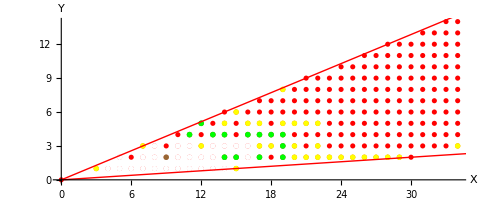

```mathematica
Plot2DSemigAll[goodExample[[1]],goodExample[[2]]]
```

```mathematica
(* Vectores de los rayos extremales para sacar ecuaciones del*)
semig=goodExample[[1]];
T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&]
```

{{15,1},{7,3}}

### Huecos, huecos pseudo-Frobenius y especiales

```mathematica
Print["G(S) -> ",goodExample[[2]]]
gS = Length[goodExample[[2]]];
Print["g(S) -> ",Length[goodExample[[2]]]]

pseuFrobs = GetPseudoFrobenius[goodExample[[1]],goodExample[[2]]];
tS=Length[pseuFrobs];
Print["PF(S) -> ",pseuFrobs]
Print["t(S) -> ",tS]

espGaps=GetEspGaps[pseuFrobs,goodExample[[2]]];
Print["SG(S) -> ",espGaps]

espGaps == pseuFrobs
```

G(S) -> {{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,3},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}

g(S) -> 40

PF(S) -> {{9,2},{11,4},{12,5},{13,4},{14,2},{14,4},{15,2},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}

t(S) -> 14

SG(S) -> {{11,4},{12,5},{13,4},{14,2},{14,4},{15,2},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}

False

### Vector Frobenius y N(S) en distintos órdenes

```mathematica
Print["Empleando orden Lexicográfico:"]
Print["v. Frob -> ",FrobeniusLexi[goodExample[[2]]]]
nLexi = NFrobeniusLexi[goodExample[[1]],goodExample[[2]]]

Print["Empleando orden Lexicográfico graduado:"]
Print["v. Frob -> ",FrobeniusDLexi[goodExample[[2]]]]
nDLexi = NFrobeniusDLexi[goodExample[[1]],goodExample[[2]]]

Print["Empleando orden Lexicográfico graduado inverso:"]
Print["v. Frob -> ",FrobeniusDRLexi[goodExample[[2]]]]
nDRLexi = NFrobeniusDRLexi[goodExample[[1]],goodExample[[2]]]

nLexi == nDLexi
nDLexi == nDRLexi
nLexi == nDRLexi
```

Empleando orden Lexicográfico:

v. Frob -> {19,4}

{{3,1},{6,2},{7,3},{9,3},{10,4},{12,3},{12,4},{13,5},{14,5},{14,6},{15,1},{15,4},{15,5},{15,6},{16,5},{16,6},{17,3},{17,5},{17,6},{17,7},{18,2},{18,3},{18,5},{18,6},{18,7}}

Empleando orden Lexicográfico graduado:

v. Frob -> {19,4}

{{3,1},{6,2},{7,3},{9,3},{10,4},{12,3},{12,4},{13,5},{14,5},{14,6},{15,1},{15,4},{15,5},{15,6},{16,5},{16,6},{17,3},{17,5},{17,6},{18,2},{18,3},{18,5},{20,2}}

Empleando orden Lexicográfico graduado inverso:

v. Frob -> {19,4}

{{3,1},{6,2},{7,3},{9,3},{10,4},{12,3},{12,4},{13,5},{14,5},{14,6},{15,1},{15,4},{15,5},{15,6},{16,5},{16,6},{17,3},{17,5},{17,6},{18,2},{18,3},{18,5},{20,2}}

False

True

False

### Desigualdad g(S) ≤ t(S)·n(S)

```mathematica
gS <= tS * Length[nLexi]
gS <= tS * Length[nDLexi]
gS <= tS * Length[nDRLexi]
```

True

True

True

Capítulo 3

Estos  dos  ejemplos  son  obtenidos  a  partir  del  algoritmo  3  aplicado  a  un  C-semigrupo.

## Ejemplo 3.1 en N.b2

### Semigrupo

```mathematica
simExample={{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,3},{8,1},{8,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,1}},{{5,2}}},1}
```

{{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,3},{8,1},{8,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,1}},{{5,2}}},1}

Vectores de los rayos extremales= {{15,1},{7,3}}

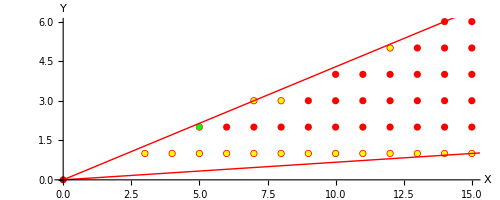

```mathematica
Plot2DSemigAll[simExample[[1,1]],simExample[[1,2]]];
```

### Huecos, huecos pseudo-Frobenius y especiales

```mathematica
Print["G(S) -> ",simExample[[1,2]]]
simgS = Length[simExample[[1,2]]];
Print["g(S) -> ",Length[simExample[[1,2]]]]

simpseuFrobs = GetPseudoFrobenius[simExample[[1,1]],simExample[[1,2]]];
simtS = Length[simpseuFrobs];
Print["PF(S) -> ",simpseuFrobs]
Print["t(S) -> ",simtS]

simespGaps=GetEspGaps[simpseuFrobs,simExample[[1,2]]];
Print["SG(S) -> ",simespGaps]

simespGaps == simpseuFrobs
```

G(S) -> {{5,2}}

g(S) -> 1

PF(S) -> {{5,2}}

t(S) -> 1

SG(S) -> {{5,2}}

True

### Vector Frobenius y N(S) en distintos órdenes

Al existir sólo un hueco, este será el vector Frobenius para cualquier orden fijado.

```mathematica
simVFrob = simExample[[1,2,1]]
simnLexi = NFrobeniusLexi[simExample[[1,1]],simExample[[1,2]]]
```

{5,2}

{{3,1},{4,1},{5,1}}

### Ap(S,b) para distintos órdenes

```mathematica
(*Punto y directorio del archivo*)
fileDirectory=NotebookDirectory[];

simApery=GetApery[simExample[[1,1]][[1]],simExample[[1,1]],simExample[[1,2]],fileDirectory]

simSubstractApery = Table[simApery[[i]] - simExample[[1,1]][[1]],{i,1,Length[simApery]}]

MemberQ[simSubstractApery,simVFrob]
```

{{8,3}}

{{5,2}}

True

### I(F(S)) y ℱ(S) para distintos órdenes

```mathematica
fileDirectory=NotebookDirectory[];

simIFS = GetIsetNoEq[simExample[[1,2,1]],simExample[[1,1]],simExample[[1,2]],fileDirectory]
Length[simIFS]

simℱS = Length[simIFS] + simgS
```

{{0,0}}

1

2

```mathematica
Length[simIFS] <= simgS
simgS == Length[simIFS]
```

True

True

```mathematica
2*simgS == simℱS
```

True

## Ejemplo 3.2 en N.b2

### Semigrupo

```mathematica
psimExample={{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{12,1},{13,1},{15,1},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},0}
```

{{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{12,1},{13,1},{15,1},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},0}

Vectores de los rayos extremales= {{15,1},{7,3}}

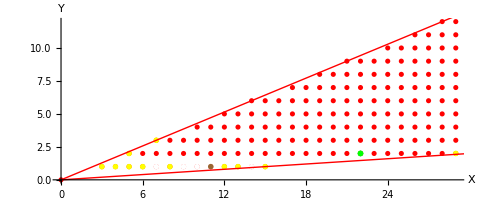

```mathematica
Plot2DSemigAll[psimExample[[1,1]],psimExample[[1,2]]]
```

### Huecos, huecos pseudo-Frobenius y especiales

```mathematica
Print["G(S) -> ", psimExample[[1,2]]]
psimgS = Length[psimExample[[1,2]]];
Print["g(S) -> ", Length[psimExample[[1,2]]]]

psimpseuFrobs = GetPseudoFrobenius[psimExample[[1,1]], psimExample[[1,2]]];
psimtS = Length[psimpseuFrobs];
Print["PF(S) -> ", psimpseuFrobs]
Print["t(S) -> ", psimtS]

psimespGaps=GetEspGaps[psimpseuFrobs, psimExample[[1,2]]];
Print["SG(S) -> ", psimespGaps]

psimespGaps == psimpseuFrobs
```

G(S) -> {{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}

g(S) -> 6

PF(S) -> {{11,1},{22,2}}

t(S) -> 2

SG(S) -> {{22,2}}

False

### Vector Frobenius y N(S) en distintos órdenes

```mathematica
Print["Empleando orden Lexicográfico:"]
Print["v. Frob -> ",FrobeniusLexi[psimExample[[1,2]]]]
psimnLexi = NFrobeniusLexi[psimExample[[1,1]],psimExample[[1,2]]]

Print["Empleando orden Lexicográfico graduado:"]
Print["v. Frob -> ",FrobeniusDLexi[psimExample[[1,2]]]]
psimnDLexi = NFrobeniusDLexi[psimExample[[1,1]],psimExample[[1,2]]]

Print["Empleando orden Lexicográfico graduado inverso:"]
Print["v. Frob -> ",FrobeniusDRLexi[psimExample[[1,2]]]]
psimnDRLexi = NFrobeniusDRLexi[psimExample[[1,1]],psimExample[[1,2]]]

psimVFrob={22,2}

psimnLexi == psimnDLexi
psimnDLexi == psimnDRLexi
psimnLexi == psimnDRLexi
```

Empleando orden Lexicográfico:

v. Frob -> {22,2}

{{3,1},{4,1},{5,1},{5,2},{6,1},{6,2},{7,2},{7,3},{8,1},{8,2},{8,3},{9,2},{9,3},{10,2},{10,3},{10,4},{11,2},{11,3},{11,4},{12,1},{12,2},{12,3},{12,4},{12,5},{13,1},{13,2},{13,3},{13,4},{13,5},{14,2},{14,3},{14,4},{14,5},{14,6},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{16,2},{16,3},{16,4},{16,5},{16,6},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{21,2},{21,3},{21,4},{21,5},{21,6},{21,7},{21,8},{21,9}}

Empleando orden Lexicográfico graduado:

v. Frob -> {22,2}

{{3,1},{4,1},{5,1},{5,2},{6,1},{6,2},{7,2},{7,3},{8,1},{8,2},{8,3},{9,2},{9,3},{10,2},{10,3},{10,4},{11,2},{11,3},{11,4},{12,1},{12,2},{12,3},{12,4},{12,5},{13,1},{13,2},{13,3},{13,4},{13,5},{14,2},{14,3},{14,4},{14,5},{14,6},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{16,2},{16,3},{16,4},{16,5},{16,6},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{18,2},{18,3},{18,4},{18,5},{18,6},{19,2},{19,3},{19,4},{19,5},{20,2},{20,3},{20,4},{21,2},{21,3}}

Empleando orden Lexicográfico graduado inverso:

v. Frob -> {22,2}

{{3,1},{4,1},{5,1},{5,2},{6,1},{6,2},{7,2},{7,3},{8,1},{8,2},{8,3},{9,2},{9,3},{10,2},{10,3},{10,4},{11,2},{11,3},{11,4},{12,1},{12,2},{12,3},{12,4},{12,5},{13,1},{13,2},{13,3},{13,4},{13,5},{14,2},{14,3},{14,4},{14,5},{14,6},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{16,2},{16,3},{16,4},{16,5},{16,6},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{18,2},{18,3},{18,4},{18,5},{18,6},{19,2},{19,3},{19,4},{19,5},{20,2},{20,3},{20,4},{21,2},{21,3}}

{22,2}

False

True

False

### Ap(S,b) para distintos órdenes

```mathematica
(*Punto y directorio del archivo*)
fileDirectory=NotebookDirectory[];

psimApery=GetApery[psimExample[[1,1]][[4]],psimExample[[1,1]],psimExample[[1,2]],fileDirectory]

psimSubstractApery = Table[psimApery[[i]] - psimExample[[1,1]][[4]],{i,1,Length[psimApery]}]

MemberQ[psimSubstractApery,psimVFrob]
MemberQ[psimSubstractApery,psimVFrob/2]
```

{{12,3},{14,3},{15,3},{16,3},{19,3},{27,4}}

{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}

True

True

### I(F(S)) y ℱ(S) para distintos órdenes

```mathematica
fileDirectory=NotebookDirectory[];

psimIFS=GetIsetNoEq[{22,2},psimExample[[1,1]],psimExample[[1,2]],fileDirectory]
Length[psimIFS]

psimℱS = Length[psimIFS] + psimgS
```

{{0,0},{8,1},{12,1},{13,1},{15,1}}

5

11

```mathematica
Length[psimIFS] <= psimgS
psimgS == Length[psimIFS] + 1
```

True

True

```mathematica
2*psimgS == 1 + psimℱS
```

True

{{15,1},{7,3}}

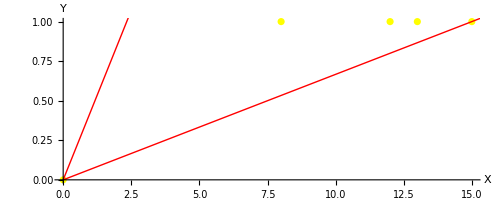

```mathematica
(* Vectores de los rayos extremales para sacar ecuaciones del*)
semig=psimExample[[1,1]];
T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&]

(*Representación gráfica Apery*)
vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];

Print[
Show[
{
ListPlot[psimIFS,PlotStyle->Yellow],
Graphics[{Red,Thick,Line[vectorsinrays]}]
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
]
];
```

Capítulo 4

## Ejecución Ejemplos 4.1 y 4.2 en N.b2

### Ejemplo base

{{{{3,1},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2},{11,3}},{{4,1},{5,1},{5,2},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1},{22,2}}},{{-1,15},{3,-7}}}

Vectores de los rayos extremales= {{15,1},{7,3}}

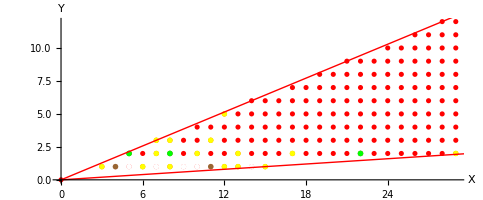

Huecos -> 10

Ps -> 5

{{5,2},{8,2},{22,2}}

Sg -> 3

```mathematica
pruebaConPseudos={{{{3,1},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2},{11,3}},{{4,1},{5,1},{5,2},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1},{22,2}}},{{-1,15},{3,-7}}}

Plot2DSemigAll[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]]];

Print["Huecos -> ",Length[pruebaConPseudos[[1,2]]]]
p = GetPseudoFrobenius[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]]];
Print["Ps -> ",Length[ GetPseudoFrobenius[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]]]]];
GetEspGaps[p,pruebaConPseudos[[1,2]]]
Print["Sg -> ",Length[ GetEspGaps[p,pruebaConPseudos[[1,2]]]]]
```

### GetIrreducibles

```mathematica
Timing [testirr = GetIrreducibles[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]],pruebaConPseudos[[2]],False]];
Length[testirr]
```

Out getsinfo -> {{1,3,5,8,10},{3,5,10},3}

N.ba de #C 3

N.ba de #C 8

N.ba de #C 23

N.ba de #C 47

N.ba de #C 71

N.ba de #C 76

N.ba de #C 56

N.ba de #C 28

10

### GetMinimalsIrreducibles

```mathematica
Timing [testminirr = GetMinimalsIrreducibles[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]],pruebaConPseudos[[2]],False,False]]
Length[testminirr]
Length[testirr]
```

Out getsinfo -> {{1,3,5,8,10},{3,5,10},3}

N.ba de #C 3

N.ba de #C 8

N.ba de #C 23

N.ba de #C 47

N.ba de #C 71

N.ba de #C 76

N.ba de #C 56

N.ba de #C 28

{0.889577,{{{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{12,1},{13,1},{15,1},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},0},{{{{3,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1}},{{4,1},{5,1},{8,2}}},0},{{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,3},{8,1},{8,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,1}},{{5,2}}},1}}}

3

10

## Ejemplo 4.1 en N.b2

### Descomposicion simple

```mathematica
pruebaConPseudos={{{3,1},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2},{11,3}},{{4,1},{5,1},{5,2},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1},{22,2}}};
```

```mathematica
testirr={{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}},0},{{{3,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{8,2}},0},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{11,1}},1},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{14,1}},1},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{10,1}},1},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{9,1}},1},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{7,1}},1},{{{3,1},{4,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{5,1}},1},{{{3,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{4,1}},1},{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{5,2}},1}};
```

### Graficando irreducibles

```mathematica
Table[Plot2DSemigAllBW[testirr[[i,1]],testirr[[i,2]]],{i,1,Length[testirr]}];
```

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

### C(S_i) ∀ i∈[t]

```mathematica
Table[IrreducibleCSi[pruebaConPseudos, testirr[[i,2]]],{i,Length[testirr]}]
```

{{{22,2}},{{8,2}},{},{},{},{},{},{},{},{{5,2}}}

## Ejemplo 4.2 en N.b2

### Descomposicion simple

```mathematica
pruebaConPseudos={{{3,1},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2},{11,3}},{{4,1},{5,1},{5,2},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1},{22,2}}};
```

```mathematica
testminirr={{{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{12,1},{13,1},{15,1},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},0},{{{{3,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1}},{{4,1},{5,1},{8,2}}},0},{{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,3},{8,1},{8,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,1}},{{5,2}}},1}}
testminirr=Table[{testminirr[[i,1,1]],testminirr[[i,1,2]],testminirr[[i,2]]},{i,1,Length[testminirr]}]
```

{{{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{12,1},{13,1},{15,1},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},0},{{{{3,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1}},{{4,1},{5,1},{8,2}}},0},{{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,3},{8,1},{8,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,1}},{{5,2}}},1}}

{{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{12,1},{13,1},{15,1},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}},0},{{{3,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1}},{{4,1},{5,1},{8,2}},0},{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,3},{8,1},{8,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,1}},{{5,2}},1}}

### Graficando irreducibles

Vectores de los rayos extremales= {{15,1},{7,3}}

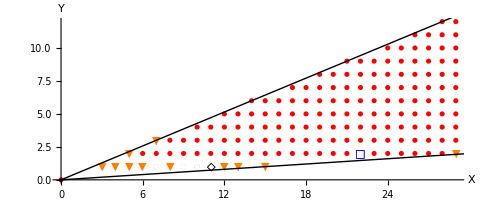

Vectores de los rayos extremales= {{15,1},{7,3}}

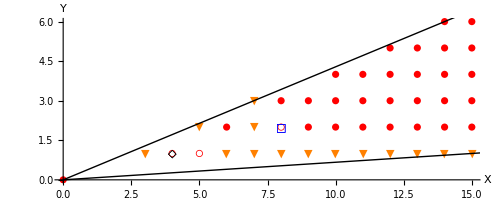

Vectores de los rayos extremales= {{15,1},{7,3}}

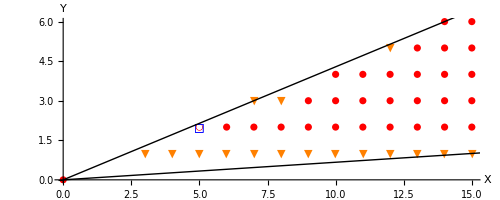

{Null,Null,Null}

```mathematica
Table[Plot2DSemigAllBW[testminirr[[i,1]],testminirr[[i,2]]],{i,1,Length[testminirr]}];
```

### C(S_i) ∀ i∈[t]

```mathematica
Table[IrreducibleCSi[pruebaConPseudos, testminirr[[i,2]]],{i,Length[testminirr]}]
espGaps = GetEspGaps[GetPseudoFrobenius[pruebaConPseudos[[1]],pruebaConPseudos[[2]]],pruebaConPseudos[[2]]]
```

{{{22,2}},{{8,2}},{{5,2}}}

{{5,2},{8,2},{22,2}}

Capítulo 5

## Ejemplo 5.1 en N.b2

```mathematica
fileDirectory=NotebookDirectory[];
```

### X conjunto de huecos de un C-semigrupo

```mathematica
coneVectors = {{15,1},{7,3}};
```

```mathematica
cminusX11={{{3,1},{7,3},{12,3},{14,5},{15,1},{15,6},{16,5},{17,3},{17,5},{18,3},{19,5},{19,8},{20,2},{20,3},{20,5},{21,2},{21,5},{22,2},{22,3},{23,2},{24,2},{25,2},{26,2},{27,2},{28,2},{29,2},{34,3},{22,5}},
{{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,3},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}};
```

{{{0,0},{300,20}},{{0,0},{140,60}}}

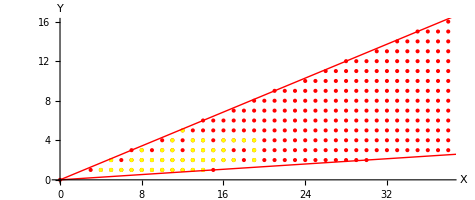

```mathematica
Plot2DConeDots[cminusX11[[2]],coneVectors]
```

```mathematica
IsSetMinusCS[cminusX11[[2]],coneVectors,fileDirectory,False,False]
```

True

### X con elementos de fuera del cono

```mathematica
coneVectors = {{15,1},{7,3}};
```

```mathematica
cminusX12 = {{15,1},{15,6},{16,5},{17,3},{17,5},{23,2},{20,1}};
```

{{{0,0},{92/3,0}},{{0,0},{92/3,184/3}}}

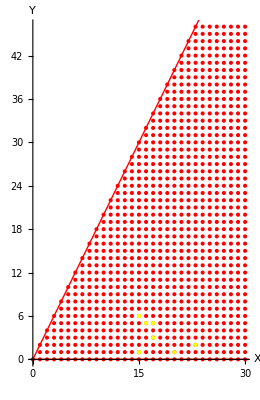

```mathematica
Plot2DConeDotsBigValues[cminusX12,coneVectors]
```

```mathematica
IsSetMinusCS[cminusX12,coneVectors,fileDirectory,True,False]
```

Exist element out of cone ->True

False

### X con condición x-a ∉ S

```mathematica
coneVectors = {{15,1},{7,3}};
```

```mathematica
cminusX13 = {{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}};
```

{{{0,0},{76/3,0}},{{0,0},{76/3,152/3}}}

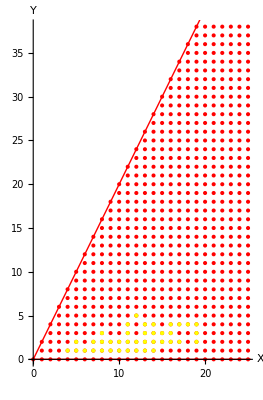

```mathematica
Plot2DConeDotsBigValues[cminusX13,coneVectors]
```

```mathematica
IsSetMinusCS[cminusX13,coneVectors,fileDirectory,True,False]
```

X subset Cone

X not void

X = D(X)

X ordered

x-a not in X ->{13,4}-{3,1}

False

### X con condición X ≠ D(X) 1

```mathematica
cminusX14 = {{7,3},{13,2},{15,1}};
```

{{{0,0},{20,0}},{{0,0},{20,40}}}

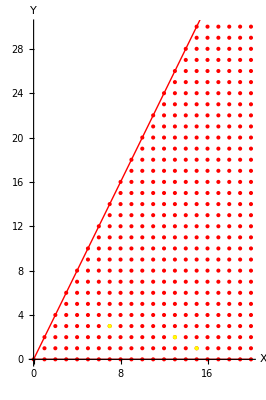

```mathematica
Plot2DConeDotsBigValues[cminusX14,coneVectors]
```

```mathematica
IsSetMinusCS[cminusX14,coneVectors,fileDirectory,True,False]
```

X subset Cone

X not void

X = D(X)

X ordered

x-a not in X ->{13,2}-{3,1}

False

### X con condición X ≠ D(X) 2

```mathematica
coneVectors = {{15,1},{7,3}};
```

```mathematica
coneVectors = {{1,0},{1,2}};
```

```mathematica
cminusX14 = {{2,0},{2,1}};
```

```mathematica
IsSetMinusCS[cminusX14,coneVectors,fileDirectory,True,True]
```

InCone[x,Eq]->{2,0}True

Exist element out of cone ->True

False

{{{0,0},{10,0}},{{0,0},{10,20}}}

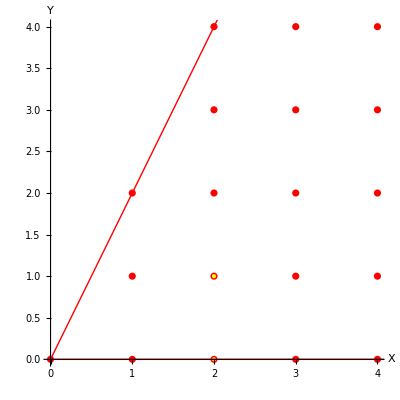

```mathematica
Plot2DConeDotsSmallValues[cminusX14,coneVectors]
```

## Ejemplo 5.2 en N.b2

```mathematica
fileDirectory=NotebookDirectory[];
```

### Vectores del cono generado por ⟨(1,0), (1,1), (1,2)⟩

```mathematica
genCone = {{1,0},{1,1},{1,2}};
```

```mathematica
(* Vectores de los rayos extremales para sacar ecuaciones del*)
semig=genCone;
T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&]

(*Representación gráfica Apery*)
vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];
```

{{1,0},{1,2}}

```mathematica
coneVectors = {{1,0},{1,2}}; (*Obtenidos a partir del siguiente apartado*)
```

### Vectores del cono generado por ⟨(1,0), (1,1), (1,2)⟩

```mathematica
X = {{1,0},{1,1},{1,2},{2,0},{2,1},{2,2},{2,3},{2,4}};
```

## Ejemplo 5.3 en N.b2

Capítulo 6

## Ejemplo 6.1 en N.b2